```mathematica
ClearAll["Global`*"];
```

CemtroidPC1 = {517.,778.857,1.}

CemtroidPC2 = {813.857,900.286,1.}

Mean[IntermediatePC1] = {0.,0.}

Mean[IntermediatePC2] = {0.,0.}

MeanDistPC1 = 393.805

MeanDistPC2 = 365.418

(0.00359115 | 0. | -1.85663
0. | 0.00359115 | -2.79699
0. | 0. | 1.)

Matrix normalization PC1= {{-1.32154,-2.15059},{-1.27845,-1.80943},{-1.40055,-1.37849},{-1.18149,0.345264},{-1.38618,0.549959},{-0.77928,0.514048},{0.359115,0.528412},{-0.308839,0.840843},{0.606905,0.226756},{0.599722,0.686423},{0.847512,0.33449},{1.75966,0.230347},{1.72734,0.388357},{1.75607,0.693605}}

1.41421

(0.00387013 | 0. | -3.14973
0. | 0.00387013 | -3.48422
0. | 0. | 1.)

Matrix normalization PC2 = {{-1.41978,-1.88199},{-1.37334,-1.58399},{-1.49719,-1.19698},{-1.33464,0.347206},{-1.49332,0.544582},{-0.943758,0.48266},{0.0431243,0.455569},{0.283072,0.7884},{0.793929,0.18466},{0.793929,0.587154},{1.00679,0.285284},{1.72276,0.157569},{1.69954,0.293024},{1.71889,0.536842}}

1.41421

Begin Computation of Fundamentalmatrix________________________________________________

CoefficientMtx = (1.87631 | 3.05337 | -1.41978 | 2.48713 | 4.04738 | -1.88199 | -1.32154 | -2.15059 | 1.
1.75575 | 2.48496 | -1.37334 | 2.02505 | 2.86611 | -1.58399 | -1.27845 | -1.80943 | 1.
2.09688 | 2.06386 | -1.49719 | 1.67642 | 1.65002 | -1.19698 | -1.40055 | -1.37849 | 1.
1.57686 | -0.460803 | -1.33464 | -0.41022 | 0.119877 | 0.347206 | -1.18149 | 0.345264 | 1.
2.07001 | -0.821263 | -1.49332 | -0.754891 | 0.299498 | 0.544582 | -1.38618 | 0.549959 | 1.
0.735452 | -0.485137 | -0.943758 | -0.376127 | 0.24811 | 0.48266 | -0.77928 | 0.514048 | 1.
0.0154866 | 0.0227874 | 0.0431243 | 0.163602 | 0.240728 | 0.455569 | 0.359115 | 0.528412 | 1.
-0.0874237 | 0.238019 | 0.283072 | -0.243489 | 0.66292 | 0.7884 | -0.308839 | 0.840843 | 1.
0.481839 | 0.180028 | 0.793929 | 0.112071 | 0.0418728 | 0.18466 | 0.606905 | 0.226756 | 1.
0.476137 | 0.544971 | 0.793929 | 0.352129 | 0.403036 | 0.587154 | 0.599722 | 0.686423 | 1.
0.853263 | 0.33676 | 1.00679 | 0.241781 | 0.0954246 | 0.285284 | 0.847512 | 0.33449 | 1.
3.03148 | 0.396832 | 1.72276 | 0.277269 | 0.0362956 | 0.157569 | 1.75966 | 0.230347 | 1.
2.93569 | 0.660029 | 1.69954 | 0.506153 | 0.113798 | 0.293024 | 1.72734 | 0.388357 | 1.
3.0185 | 1.19223 | 1.71889 | 0.942734 | 0.372356 | 0.536842 | 1.75607 | 0.693605 | 1.)

Rank CoefficientMatx = 9

FFin = (0.00395443 | -0.0614908 | 0.0177982
0.0976574 | -0.0023792 | 0.751453
-0.0024786 | -0.649249 | -0.0114927)

FFin Rank = 3

PC2NormTest = {{-1.41978,-1.88199,1.},{-1.37334,-1.58399,1.},{-1.49719,-1.19698,1.},{-1.33464,0.347206,1.},{-1.49332,0.544582,1.},{-0.943758,0.48266,1.},{0.0431243,0.455569,1.},{0.283072,0.7884,1.},{0.793929,0.18466,1.},{0.793929,0.587154,1.},{1.00679,0.285284,1.},{1.72276,0.157569,1.},{1.69954,0.293024,1.},{1.71889,0.536842,1.}}

PC1NormTest = {{-1.32154,-2.15059,1.},{-1.27845,-1.80943,1.},{-1.40055,-1.37849,1.},{-1.18149,0.345264,1.},{-1.38618,0.549959,1.},{-0.77928,0.514048,1.},{0.359115,0.528412,1.},{-0.308839,0.840843,1.},{0.606905,0.226756,1.},{0.599722,0.686423,1.},{0.847512,0.33449,1.},{1.75966,0.230347,1.},{1.72734,0.388357,1.},{1.75607,0.693605,1.}}

l = {{{0.127909,0.617278,1.21391},{0.109768,0.621104,1.02031},{0.0854806,0.608089,0.769353},{-0.0088295,0.620289,-0.233608},{-0.0215938,0.604324,-0.361361},{-0.015613,0.658139,-0.32252},{-0.0100446,0.75458,-0.307378},{-0.0295618,0.777221,-0.524062},{0.00958281,0.828546,-0.133351},{-0.0151668,0.827589,-0.394669},{0.00423713,0.849094,-0.199208},{0.0149216,0.919318,-0.118065},{0.00650061,0.916728,-0.205951},{-0.00841542,0.918038,-0.364297}}}

lPrime = {{{-0.217725,-0.56287,-1.65108},{-0.184238,-0.566331,-1.39395},{-0.142637,-0.559849,-1.07229},{0.0265668,-0.57742,0.226928},{0.0457474,-0.56532,0.377104},{0.0446403,-0.602554,0.36092},{0.0505449,-0.672589,0.391976},{0.0784146,-0.632259,0.614864},{0.0220657,-0.687108,0.169705},{0.0669272,-0.68776,0.514996},{0.0335383,-0.702159,0.254945},{0.0269749,-0.758,0.192921},{0.042278,-0.756389,0.311083},{0.0722013,-0.758882,0.540974}}}

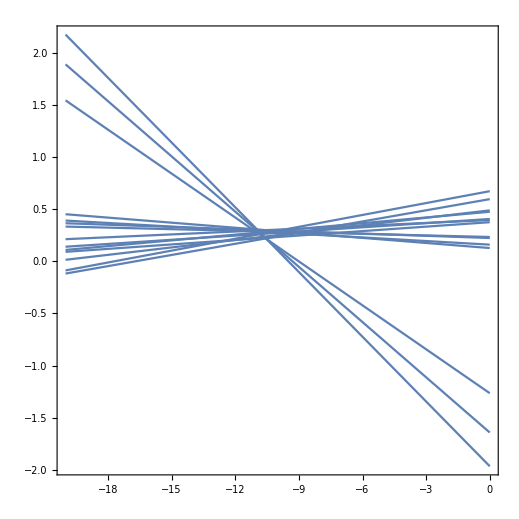

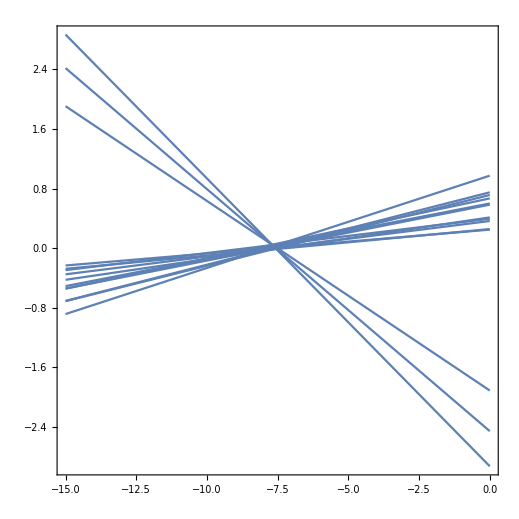

FPrime MatrixRank = 2

FPrime = (0.00226486 | -0.0614886 | 0.0180179
0.0977003 | -0.00237926 | 0.751447
-0.00231874 | -0.649249 | -0.0115135)

2

lRank2 = {{{0.130523,0.617212,1.21366},{0.112305,0.62104,1.02007},{0.0882273,0.608019,0.769093},{-0.00635412,0.620226,-0.233842},{-0.0188499,0.604254,-0.36162},{-0.0137977,0.658093,-0.322692},{-0.0098968,0.754576,-0.307392},{-0.0298187,0.777228,-0.524038},{0.00846149,0.828575,-0.133245},{-0.0162873,0.827617,-0.394563},{0.00275639,0.849132,-0.199068},{0.0122309,0.919386,-0.11781},{0.00384944,0.916795,-0.2057},{-0.0110988,0.918106,-0.364043}}}

lPrime = {{{-0.215425,-0.562873,-1.65138},{-0.181996,-0.566334,-1.39424},{-0.14017,-0.559852,-1.07261},{0.0287377,-0.577423,0.226646},{0.0482729,-0.565323,0.376776},{0.0461389,-0.602556,0.360725},{0.0501207,-0.672588,0.392031},{0.0791324,-0.63226,0.614771},{0.0212099,-0.687107,0.169816},{0.0661033,-0.687759,0.515103},{0.0322806,-0.702158,0.255109},{0.0241716,-0.757997,0.193285},{0.0395361,-0.756385,0.31144},{0.069424,-0.758878,0.541335}}}

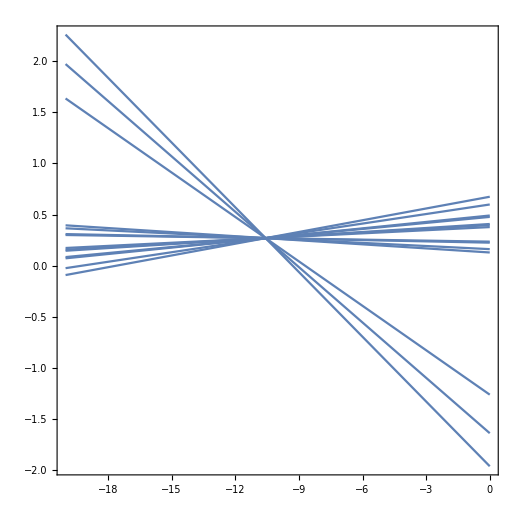

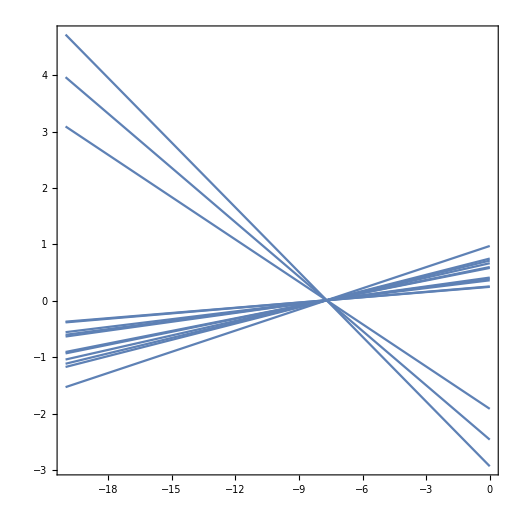

Demnormalized FPrime -> F =(3.14775×10^-8 | -8.54582×10^-7 | 0.000719055
1.35786×10^-6 | -3.30674×10^-8 | 0.00223194
-0.00125641 | -0.00160628 | -0.785851)

F Rank = 2

-0.0021118

-0.00659881

-0.00201548

-0.00453507

-0.00232076

-0.00360466

0.00174071

0.000627814

-0.00620289

-0.00203104

0.0064902

-0.00623247

-0.00160033

-0.00678194

lRank2De = {{{0.000379328,0.00282521,-2.01246},{0.000313903,0.00283896,-2.15122},{0.000227438,0.0027922,-2.27165},{-0.000112218,0.00283604,-2.96532},{-0.000157093,0.00277868,-2.99573},{-0.00013895,0.00297202,-3.14843},{-0.000124941,0.00331851,-3.45757},{-0.000196483,0.00339985,-3.67361},{-0.0000590134,0.00358425,-3.58888},{-0.00014789,0.00358081,-3.75593},{-0.0000795013,0.00365807,-3.69974},{-0.0000454767,0.00391037,-3.87917},{-0.0000755759,0.00390106,-3.92785},{-0.000129257,0.00390577,-4.03533}}}

lPrimeRank2De = {{{-0.0010073,-0.00173956,-0.276963},{-0.000877928,-0.00175296,-0.0563002},{-0.000716055,-0.00172787,0.187084},{-0.0000623618,-0.00179587,1.30228},{0.000013242,-0.00174904,1.38851},{4.98307×10^-6,-0.00189314,1.48771},{0.0000203929,-0.00216417,1.72458},{0.000132672,-0.0020081,1.78501},{-0.0000914954,-0.00222036,1.58671},{0.0000822477,-0.00222288,1.87096},{-0.0000486506,-0.00227861,1.70185},{-0.0000800333,-0.00249472,1.81976},{-0.0000205707,-0.00248848,1.91149},{0.0000950992,-0.00249813,2.10696}}}

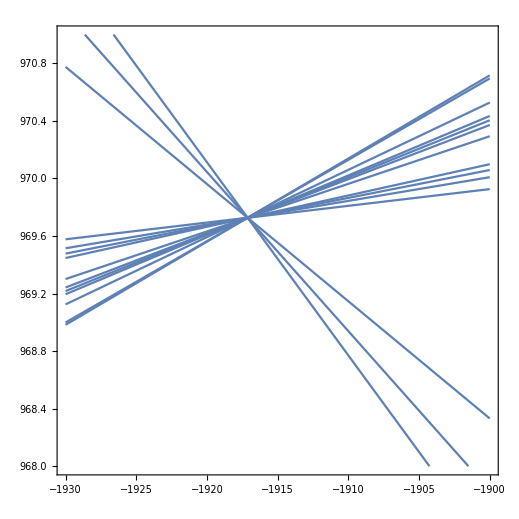

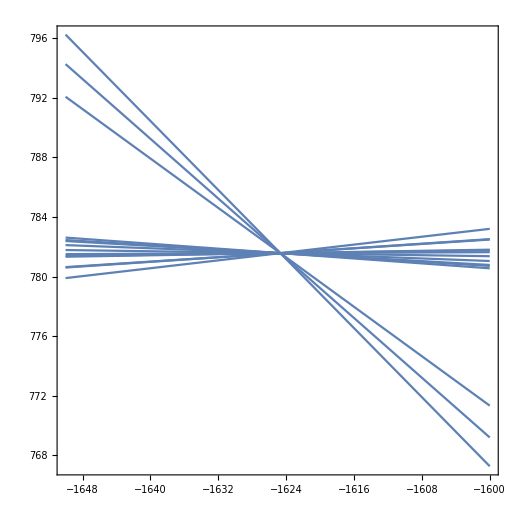

epipole ={-0.90115,0.433506,0.000554662}

epipolePrime = {0.892339,-0.451366,-0.000465457}

Test F^T.e' = {0,0,0}

Test F.e = {0,0,0}

End Computation of Fundamentalmatrix________________________________________________

Begin Computation of Essential Matrix with K1 and K2___________________________________

PC1mm = (149. | 180. | 1.
161. | 275. | 1.
127. | 395. | 1.
188. | 875. | 1.
131. | 932. | 1.
300. | 922. | 1.
617. | 926. | 1.
431. | 1013. | 1.
686. | 842. | 1.
684. | 970. | 1.
753. | 872. | 1.
1007. | 843. | 1.
998. | 887. | 1.
1006. | 972. | 1.)

PC2mm = (447. | 414. | 1.
459. | 491. | 1.
427. | 591. | 1.
469. | 990. | 1.
428. | 1041. | 1.
570. | 1025. | 1.
825. | 1018. | 1.
887. | 1104. | 1.
1019. | 948. | 1.
1019. | 1052. | 1.
1074. | 974. | 1.
1259. | 941. | 1.
1253. | 976. | 1.
1258. | 1039. | 1.)

PC1 in mm = (149. | 180. | 1.
161. | 275. | 1.
127. | 395. | 1.
188. | 875. | 1.
131. | 932. | 1.
300. | 922. | 1.
617. | 926. | 1.
431. | 1013. | 1.
686. | 842. | 1.
684. | 970. | 1.
753. | 872. | 1.
1007. | 843. | 1.
998. | 887. | 1.
1006. | 972. | 1.)

PC2 in mm = (447. | 414. | 1.
459. | 491. | 1.
427. | 591. | 1.
469. | 990. | 1.
428. | 1041. | 1.
570. | 1025. | 1.
825. | 1018. | 1.
887. | 1104. | 1.
1019. | 948. | 1.
1019. | 1052. | 1.
1074. | 974. | 1.
1259. | 941. | 1.
1253. | 976. | 1.
1258. | 1039. | 1.)

normalized Coordinates K1 = (8.24989 | 10.1271 | 1.
8.9429 | 15.6121 | 1.
6.97937 | 22.5406 | 1.
10.5022 | 50.2545 | 1.
7.21037 | 53.5456 | 1.
16.9702 | 52.9682 | 1.
35.2772 | 53.1991 | 1.
24.5356 | 58.2223 | 1.
39.262 | 48.3492 | 1.
39.1465 | 55.7396 | 1.
43.1313 | 50.0813 | 1.
57.8 | 48.4069 | 1.
57.2802 | 50.9474 | 1.
57.7422 | 55.8551 | 1.)

normalized Coordinates K2 = (23.8 | 22.0989 | 1.
24.4449 | 26.2413 | 1.
22.7252 | 31.6212 | 1.
24.9823 | 53.0867 | 1.
22.7789 | 55.8304 | 1.
30.4103 | 54.9696 | 1.
44.1146 | 54.593 | 1.
47.4466 | 59.2197 | 1.
54.5406 | 50.8271 | 1.
54.5406 | 56.4222 | 1.
57.4964 | 52.2259 | 1.
67.4387 | 50.4506 | 1.
67.1163 | 52.3335 | 1.
67.385 | 55.7228 | 1.)

EsMtx = {{0.0000101421,-0.000275411,0.0133101},{0.000437048,-0.0000106457,0.0416395},{-0.0216776,-0.0278836,-0.790769}}

2

SVD of EMtx ={{{-0.0167611,0.449521,-0.893112},{-0.0524872,0.891611,0.44975},{0.998481,0.0544153,0.00864971}},{{0.792761,0.,0.},{0.,0.00182963,0.},{0.,0.,0.}},{{-0.027332,-0.429242,-0.902776},{-0.0351128,-0.902144,0.430005},{-0.99901,0.0434519,0.00958548}}}

new SVD = {{{-0.0167611,0.449521,-0.893112},{-0.0524872,0.891611,0.44975},{0.998481,0.0544153,0.00864971}},{{0.397295,0.,0.},{0.,0.397295,0.},{0.,0.,0.}},{{-0.027332,-0.429242,-0.902776},{-0.0351128,-0.902144,0.430005},{-0.99901,0.0434519,0.00958548}}}

EPrime = {{-0.0764775,-0.160882,0.0144127},{-0.151482,-0.318837,0.0362243},{-0.0201221,-0.0334324,-0.39536}}

2

-0.0021118

-0.00659881

-0.00201548

-0.00453507

-0.00232076

-0.00360466

0.00174071

0.000627814

-0.00620289

-0.00203104

0.0064902

-0.00623247

-0.00160033

-0.00678194

End Computation of Essential Matrix with K1 and K2___________________________________

Begin Reconstruction of Rotation and Translation________________________________________________

E = (-0.0764775 | -0.160882 | 0.0144127
-0.151482 | -0.318837 | 0.0362243
-0.0201221 | -0.0334324 | -0.39536)

U of E = {{-1.47944×10^-16,0.449833,0.893112},{0.0192287,0.892947,-0.44975},{-0.999815,0.0171734,-0.00864971}}

Sigma of E = {{0.397295,0.,0.},{0.,0.397295,0.},{0.,0.,0.}}

V of E = {{0.0433069,-0.427926,-0.902776},{0.0687029,-0.900209,0.430005},{0.996697,0.0806455,0.00958548}}

S1 = (0. | 0.00864971 | -0.44975
-0.00864971 | 0. | -0.893112
0.44975 | 0.893112 | 0.)

S2 = (0. | -0.00864971 | 0.44975
0.00864971 | 0. | 0.893112
-0.44975 | -0.893112 | 0.)

R1 = (-0.786799 | 0.414947 | 0.456908
0.452923 | -0.114737 | 0.884136
-0.419294 | -0.902582 | 0.0976643)

R2 = (-0.825761 | 0.353138 | -0.439787
0.359124 | -0.272053 | -0.892758
0.434912 | 0.895143 | -0.0978301)

Check if t of S1, S2 is equal = {{{0.893112,-0.44975,-0.00864971}},{{-0.893112,0.44975,0.00864971}}}

R1 is Rotation = {{1.,0,0},{0,1.,0},{0,0,1.}}

R2 is Rotation ={{1.,0,0},{0,1.,0},{0,0,1.}}

Determinant of R1 = -1.

Determinant of R2 = -1.

Left S und E = {{-0.902776,0.430005,0.00958548}} , {{-0.893112,0.44975,0.00864971}}

P1 = (0.786799 | -0.414947 | -0.456908 | -0.902776
-0.452923 | 0.114737 | -0.884136 | 0.430005
0.419294 | 0.902582 | -0.0976643 | 0.00958548)

P2 = (0.786799 | -0.414947 | -0.456908 | 0.902776
-0.452923 | 0.114737 | -0.884136 | -0.430005
0.419294 | 0.902582 | -0.0976643 | -0.00958548)

P3 = (0.825761 | -0.353138 | 0.439787 | -0.902776
-0.359124 | 0.272053 | 0.892758 | 0.430005
-0.434912 | -0.895143 | 0.0978301 | 0.00958548)

P4 = (0.825761 | -0.353138 | 0.439787 | 0.902776
-0.359124 | 0.272053 | 0.892758 | -0.430005
-0.434912 | -0.895143 | 0.0978301 | -0.00958548)

{1.11307,1.47281,-1.11853}

(0.18464 | 0.387015 | -0.0335212
0.38607 | 0.810852 | -0.0925487
0.0705603 | 0.0748477 | 0.994649)

End Reconstruction of Rotation and Translation________________________________________________

```mathematica
NormalizeCoordinates[PC1,PC2];
```